# Demonstrações no Mathematica em uma Introdução à Teoria Quântica de Campos e Física de Partículas

## Um notebook dinâmico e educacional para TQC

Por Bruno Gehlen F . da Silva

## Capítulo #1: Introdução e Teoria

## Contexto Histórico

O século XX iniciou com a grande descoberta da física quântica por Max Planck e seus estudos sobre a quantização da matéria e o Corpo Negro, permitindo descrever várias oscilações de diferentes modos confinados em uma cavidade (explicando a Catástrofe do Ultravioleta). Albert Einstein interpretou essa quantização como partículas sem massa chamadas fótons e utilizou essas novas descobertas para determinar seus Coeficientes, além do famoso Efeito Fotoelétrico. Com este novo formalismo, é possível utilizar os operadores de Aniquilação e Criação em modos de energia (ou momento) e até mesmo encontrar a Taxa de Transição entre diferentes estados quânticos.

No mesmo século, também houve enormes avanços na área da relatividade: não há um referencial absoluto, a luz viaja a uma velocidade constante e, dependendo da velocidade do observador, diferentes grandezas físicas podem ser medidas. Descobriram-se observáveis invariantes de Lorentz (simétricos por todo o Grupo de Poincaré), pois já se sabia que rotações mantinham normas inalteradas, e agora haviam os Boosts de Lorentz. Também foi descoberto que esses boosts se reduzem às transformações de referencial de Galileu no regime das baixas energias (validando ainda a física clássica tradicional), e então passou-se a lidar com objetos traduzidos como campos e operadores invariantes sob todas essas transformações, sejam elas contínuas ou discretas no universo.

Hoje em dia, a humanidade já foi capaz de conciliar ambas as teorias na então chamada de Teoria Quântica de Campos (TQC), onde, diferente da mecânica quântica usual, a quantidade de partículas do sistema pode ser modificada ao longo dos processos, sendo assim a base para diversos sistemas de diferentes áreas da física moderna, como o estudo da Matéria Condensada e a Física de Partículas em si. A maneira como a TQC é construída permite que a matriz S (de espalhamento, “scattering”) seja utilizada de forma que, tomando que as interações ocorram em um tempo muito curto comparado o resto do espalhamento e tratando os campos como operadores que criam e/ou aniquilam partículas de certos estados, é possível descrever qualquer processo onde entrem n partículas e saiam m outras.

## Formalismo Rápido

Falando propriamente sobre nossa teoria, é necessário lembrar alguns aspectos básicos da Teoria Quântica de Campos. Após a chamada “segunda quantização”, onde são estabelecidas as relações de comutação locais (em tempos iguais) entre os operadores de criação/aniquilação e a normalização dos estados, além de também definir a ação desses operadores em um estado de uma partícula:

-Graphics-

define-se que n partículas podem simultaneamente ocupar um estado de momento p, resultando na soma direta dos espaços de Hilbert das i partículas, também chamado de espaço de Fock, permitindo agora a introdução de Campos Escalares Quânticos:

-Graphics-

que são soluções da equação de Klein-Gordon e portanto podem ser decompostos em ondas planas. Processos semelhantes se aplicam em Campos Spinoriais (que descrevem férmions), o que demanda um aprofundamento no estudo das representações do Grupo de Poincaré ISO(1,3) (possui rotações, boosts de Lorentz, inversão temporal e por paridade) e sobre o que são spinores em si, e Campos Tensoriais, como do fóton e do hipotético gráviton, que exigem bases com polarizações para cada um dos índices do objeto, relacionados com spin inteiro (bósons).

É possível então deduzir as Regras de Feynman, tanto no espaço de posição quanto de momento, que ajudam durante o já bem estabelecido formalismo de Diagramas de Feynman, estes sendo representações das séries perturbativas que surgem ao calcular as funções entre n-pontos de teorias interagentes:

-Graphics-                        -Graphics-

Toda a ideia de diagramas e funções de muitos pontos facilita os cálculos pois basta que todas as amplitudes (chance de um estado inicial chegar em um estado final) que podem físicamente contribuir para o processo sejam somadas, além de sutilidades como soma sobre spins e polarizações . Além disso, é chegado um momento em que é necessário estudar o processo de Renormalização de teorias já que a inserção de loops nos diagramas, apesar de incrementar a presição, acaba criando divergências nos observáveis, o que certamente não é compatível com quase tudo observado no universo atual, e portanto é necessário deformar a teoria em uma certa escala e fazer modificações em passos intermediários dos cálculos de forma que os observáveis extraídos agora sejam finitos.

## Capítulo #2: Cálculos

## Primeiros Cálculos

Agora, iniciam-se os cálculos de alguns espalhamentos já conhecidos para avaliar a autenticidade da teoria descrita até aqui. Tomando o famoso Espalhamento de Møller, algo extremamente natural na eletrodinâmica quântica escalar, onde dois elétrons se aproximam e se repelem ao trocar um fóton:

-Graphics-

Pela Lagrangiana, nota-se que os diagramas possíveis são o canal - t e canal - u (e isso pode ser visto com o auxílio do pacote FeynArts), e então, definindo a contração de índices e grandezas necessárias (variáveis de Mandelstam) :

```mathematica
<<<<FeynArts`(*Carregamento do pacote FeynArts caso queira visualizar os diagramas*)
normLortz[x_,y_]:=(x[[1]]*y[[1]])-(x[[2]]*y[[2]])-(x[[3]]*y[[3]])-(x[[4]]*y[[4]]);
	(*com a assinatura da métrica Lorentziana dada por (+,-,-,-)*)
p1={p10,p11,p12,p13};
p2={p20,p21,p22,p23};
p3={p30,p31,p32,p33};
p4={p40,p41,p42,p43};
	(*definição dos 4-momentos inicialmente genéricos*)
```

loading generic model file /home/brunogehlen/Documentos/wolfram-qft/FeynArts-3.11/Models/QED.gen

> $GenericMixing is OFF

generic model {QED} initialized

loading classes model file /home/brunogehlen/Documentos/wolfram-qft/FeynArts-3.11/Models/QED.mod

> 7 particles (incl. antiparticles) in 2 classes

> $CounterTerms are ON

> 1 vertices

> 3 counterterms of order 1

classes model {QED} initialized

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

> Top. 2: 0 Generic, 0 Classes insertions

> Top. 3: 1 Generic, 1 Classes insertions

> Top. 4: 1 Generic, 1 Classes insertions

in total: 2 Generic, 2 Classes insertions

> Top. 1 aebf/cedf/ef.m, 0 diagrams

> Top. 2 aebf/cfde/ef.m, 0 diagrams

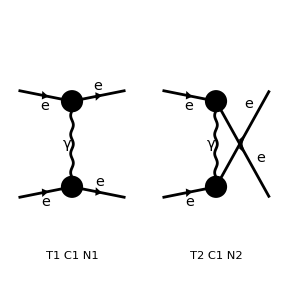

FeynArtsGraphics[{e,e}→{e,e}][([T1 C1 N1] | [T2 C1 N2]
Null | Null)]

```mathematica
sups1={e>0,g>0,λ>0,α==e^2/(4π),
normLortz[p1+p2,p1+p2]==s,
(*normLortz[p3+p4,p3+p4]==s,*)
normLortz[p1-p3,p1-p3]==t,
(*normLortz[p2-p4,p2-p4]==t,*)
normLortz[p1-p4,p1-p4]==u
(*normLortz[p2-p3,p2-p3]==u*)
};
	(*constante de acomplamento e variáveis de mandelstam; são as suposições que vão ser usadas nos cálculos*) 
sups2={
normLortz[p1+p3,p2+p4]==s-u,
(p12 p22+p13 p23-p10 (p20+p30)+p11 (p21+p31)+p12 p32+p13 p33-p20 p40-p30 p40+p21 p41+p31 p41+p22 p42+p32 p42+p23 p43+p33 p43)==s-t
};
Paint[InsertFields[CreateTopologies[0,2->2],{F[1,{1}],F[1,{1}]}->{F[1,{1}],F[1,{1}]},Model->"QED",GenericModel->"QED"],ColumnsXRows->2,PaintLevel->{Classes}](*Utilizando o pacote FeynArts para ver os possíveis diagramas para um espalhamento férmions 2->2*)
```

além dos componentes da seção de choque, sabendo que neste caso apenas haverá diagramas T e U:

```mathematica
vert[g_]:=ⅈ*g;
	(*Cada vértice dá um fator (-ⅈg)*)
propEsc[p_,m_]:=ⅈ/(normLortz[p,p]-m^2);
propFot[p_]:=-ⅈ/normLortz[p,p];
	(*O propagador depende do diagrama que contribue*)
mDiagramaQEDescalar[m_,g_,numVert_,numPropFot_,pIn_,pOut_,pPropg_]:=
(vert[g]^numVert)*
(propFot[pPropg]^numPropFot)*
(normLortz[pIn,pOut])*(ⅈ);
	(*Os fatores ⅈϵ foram retirados pois  e estamos no gauge de Feynman*)
	(*constantes como c e ℏ já estão definidos como 1*)
ℳQEDEsc=mDiagramaQEDescalar(*Um alias para diminuir o tamanho da função*);
```

```mathematica
crossSectionQEDCM[m_,g_,s_,t_,u_]:=(1/(64*π^2*normLortz[p1+p2,p1+p2]))*Abs[(ℳQEDEsc[m,g,2,1,p1+p2,p3+p4,p1+p2]*s)+(ℳQEDEsc[m,g,2,1,p1+p3,p2+p4,p1-p3]*t)+(ℳQEDEsc[m,g,2,1,p1+p4,p2+p3,p1-p4]*u)]^2;
(*O total será a soma das contribuções, e neste caso apenas os diagramas T e U*)
dσdΩ[m_,g_,s_,t_,u_]:=Simplify[Simplify[crossSectionQEDCM[m,g,s,t,u],Assumptions->sups1],Assumptions->sups2];
	(*Um alias para diminuir o tamanho da função, assumir acoplamentos positivos e assumir as variáveis de Mandelstam e suas relações*);
```

no gauge de Feynman, encontra - se que a seção de choque será dada por

```mathematica
dσdΩ[Subscript[m, e],e,0,1,1]
```

(α^2 Abs[((t-u) (-s+t+u))/(t u)]^2)/(4 s)

condizente com a literatura! Escrevendo as variáveis de Mandelstam em função do ângulo

```mathematica
sups3={t->Cos[θ]-1,u->-Cos[θ]+1,α->1/137,s->10};
```

é possível plotar a amplitude de espalhamento :

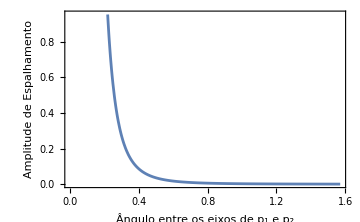

```mathematica
Plot[Evaluate[dσdΩ[Subscript[m, e],e,0,1,1]/.sups3],{θ,0,π/2},Frame->True,FrameLabel->{"Ângulo entre os eixos de p_1 e p_2","Amplitude de Espalhamento"},Ticks->Automatic,ImageSize->Medium]
```

*Implementações com o pacote FeynRules serão formuladas em futuras atualizações

## Outros Campos

Para a QED com spinores, adiciona-se a nova regra para propagadores internos spinoriais. Tomando o Espalhamento Elétron-Muon:

## Renormalização

Após estudar o processo de renormalização, é possível tentar aplica-lo para uma teoria como a QED.